{{x→InterpolatingFunction[{{0., 3.}}, <>],y→InterpolatingFunction[{{0., 3.}}, <>],ψ→InterpolatingFunction[{{0., 3.}}, <>]}}

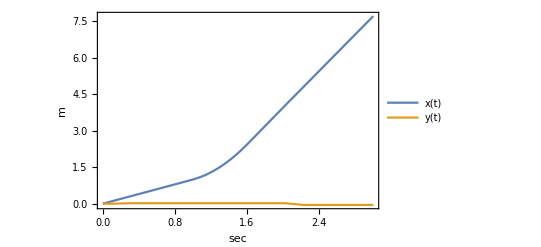

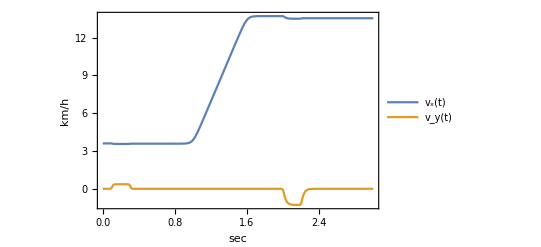

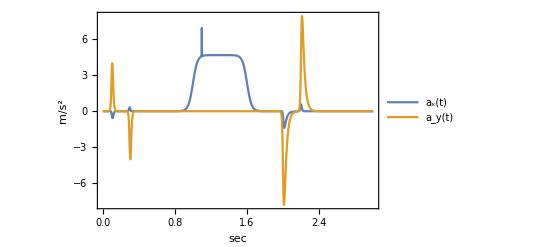

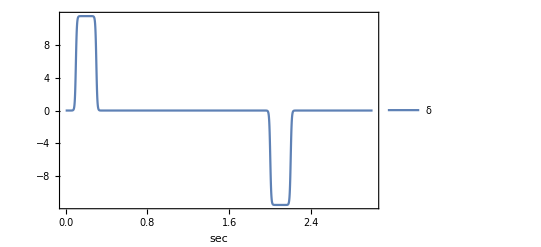

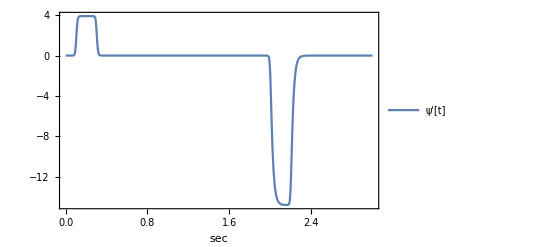

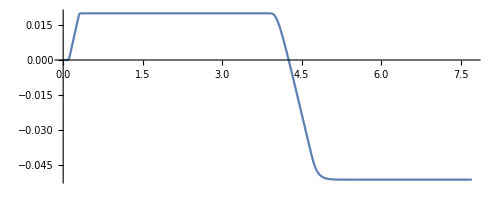

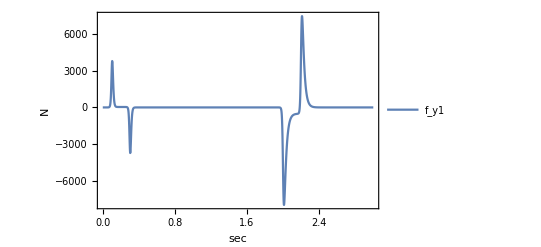

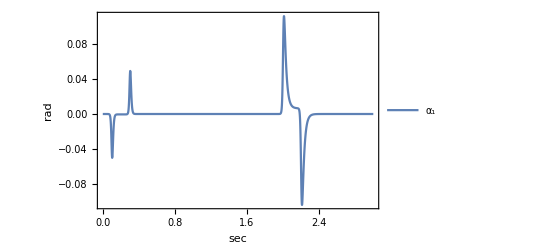

```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)]);
Brake[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
S1[t_,τ1_,δ1_]:=δ1/2*(Tanh[100t]-Tanh[100(t-τ1)]);
S2[t_,τ01_,τ1_,δ1_]:=Fold[Plus,0,Table[S1[t-τ01⟦k⟧,τ1⟦k⟧,δ1⟦k⟧],{k,1,Length[τ1]}]];
Subscript[β, r] = Brake[t,τ0 ,τ ,β];
η = √(1.0-Subscript[β, r]^2);
δ = S2[t,τ01,τ1,δ1];

rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->5000,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

Slip angle;
f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f1[Subscript[μ, 1],Subscript[F, z1],Subscript[C, α1]]; Subscript[α, sl2]=f1[Subscript[μ, 2],Subscript[F, z2],Subscript[C, α2]];
Subscript[α, sl3]=f1[Subscript[μ, 3],Subscript[F, z3],Subscript[C, α3]]; Subscript[α, sl4]=f1[Subscript[μ, 4],Subscript[F, z4],Subscript[C, α4]];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
Subscript[α, 1]=f2[δ,Subscript[l, f]]; Subscript[α, 2]=f2[δ,Subscript[l, f]];
Subscript[α, 3]=f2[0,-Subscript[l, r]]; Subscript[α, 4]=f2[0,-Subscript[l, r]];

Tire  Lateral Force;
f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{ - C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3,Abs[α]<αs},{-η μ F Sign[α],Abs[α]≥αs}}]/.rules;
Subscript[f, y1]=f3[Subscript[C, α1],Subscript[α, 1],Subscript[μ, 1],Subscript[F, z1],Subscript[α, sl1]]/.rules; Subscript[f, y2]=f3[Subscript[C, α2],Subscript[α, 2],Subscript[μ, 2],Subscript[F, z2],Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f3[Subscript[C, α3],Subscript[α, 3],Subscript[μ, 3],Subscript[F, z3],Subscript[α, sl3]]/.rules; Subscript[f, y4]=f3[Subscript[C, α4],Subscript[α, 4],Subscript[μ, 4],Subscript[F, z4],Subscript[α, sl4]]/.rules;

Tire  Longitudinal Force;
f4[μ_,F_]:=Subscript[β, r] μ F/.rules;
Subscript[f, x1]=f4[Subscript[μ, 1],Subscript[F, z1]]/.rules; Subscript[f, x2]=f4[Subscript[μ, 2],Subscript[F, z2]]/.rules;
Subscript[f, x3]=f4[Subscript[μ, 3],Subscript[F, z3]]/.rules; Subscript[f, x4]=f4[Subscript[μ, 4],Subscript[F, z4]]/.rules;

Long. and Lat. Tot. Forces;
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];

Equations of Motion;
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4];
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4];
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4]);
motionEq ={Eq1,Eq2,Eq3};

time =3;

τ0 = {1,10,20,50};
τ = {0.6,5,5,5};
β={0.1,0,0,0.0};

τ01 = {0.1,2,10,102,135 ,140};
τ1 = {0.2,0.2,0.1,4,3 ,20};
δ1={0.2,-0.2,0,0,-0.025,0.025};

initCond={x[0]==0.0,x'[0]==1,y[0]==0.0,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0.00};
solution=NDSolve[{motionEq/.rules,initCond},{x,y,ψ},{t,0,time},MaxSteps->20000]

f5[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;

f5[x[t],y[t],m,x[t],"y(t)"]
f5[x'[t]*3.6,y'[t]*3.6,"km/h","v_x(t)","v_y(t)"]
f5[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"]
f5[δ*180/π,,"","δ",""]
f5[ψ'[t]*180/π,,"","ψ'[t]",""]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},PlotRange-> All]
f5[Subscript[f, y1],,"N","f_y1",""]
f5[Subscript[α, 1],,"rad","α_1",""]
```

```mathematica
Needs["MATLink`"]
```

```mathematica
OpenMATLAB[]
```

```mathematica
CommandWindow["Show"]
```

```mathematica
MEvaluate["asd = 12321"]
```

asd =

       12321

x=1
plot(x)

x =

     1

```mathematica
MSet["n",m]
```

MSet::unsupp: Unsupported data type. The expression "m" can't be converted.

$Failed

```mathematica
MSet["A",x[t]]
```

MSet::unsupp: Unsupported data type. The expression "x[t]" can't be converted.

$Failed

```mathematica
Environment["PATH"]
```

C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Libraries\Windows-x86-64;C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Libraries\Windows;C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Kernel\Binaries\Windows-x86-64;C:\Program Files\Wolfram Research\Mathematica\10.0;C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\FrontEnd\Binaries\Windows-x86-64;C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Kernel\Binaries\Windows-x86-64;C:\ProgramData\Oracle\Java\javapath;C:\WINDOWS\system32;C:\WINDOWS;C:\WINDOWS\System32\Wbem;C:\WINDOWS\System32\WindowsPowerShell\v1.0\;C:\Program Files (x86)\Windows Kits\8.1\Windows Performance Toolkit\;C:\Program Files\Microsoft SQL Server\110\Tools\Binn\;C:\Program Files (x86)\Microsoft SDKs\TypeScript\1.0\;C:\Program Files\Microsoft SQL Server\120\Tools\Binn\;C:\Program Files\MATLAB\R2013b\polyspace\bin;C:\Program Files\MATLAB\R2013b\bin\win64;.;;.;;.;

```mathematica
MATLink`Developer`GetInfo[]
```

MATLink 1.1 for Windows (Fri 15 Aug 2014)

10.0 for Microsoft Windows (64-bit) (September 9, 2014)

Force 32-bit engine: False

System PATH:
C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Libraries\Windows-x86-64
C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Libraries\Windows
C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Kernel\Binaries\Windows-x86-64
C:\Program Files\Wolfram Research\Mathematica\10.0
C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\FrontEnd\Binaries\Windows-x86-64
C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Kernel\Binaries\Windows-x86-64
C:\ProgramData\Oracle\Java\javapath
C:\WINDOWS\system32
C:\WINDOWS
C:\WINDOWS\System32\Wbem
C:\WINDOWS\System32\WindowsPowerShell\v1.0\
 C:\Program Files (x86)\Windows Kits\8.1\Windows Performance Toolkit\
C:\Program Files\Microsoft SQL Server\110\Tools\Binn\
C:\Program Files (x86)\Microsoft SDKs\TypeScript\1.0\
C:\Program Files\Microsoft SQL Server\120\Tools\Binn\
C:\Program Files\MATLAB\R2013b\polyspace\bin
 C:\Program Files\MATLAB\R2013b\bin\win64
.

.

.


COM server information:
CLSID: {0E19A325-4FFD-41F4-9E6D-FDE6788A81EA}
Program ID: Matlab.Application (Version 8.2)
Command: C:\Program Files\MATLAB\R2013b\bin\win64\MATLAB.exe /MLAutomation

```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

```mathematica
Needs["WSMLink`"];
```

```mathematica
WSMCreateModel["newmmodela",{motionEq,initCond},t]
```

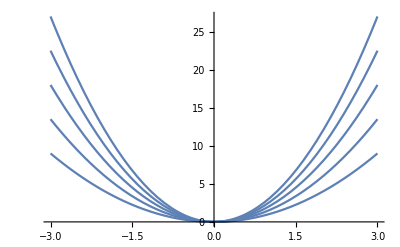

```mathematica
g[x_,y_,γ_]:=γ x^2+y
Plot3D[Table[g[x,γ],{γ,1,3,.5}],{x,-3,3},Plot]
```

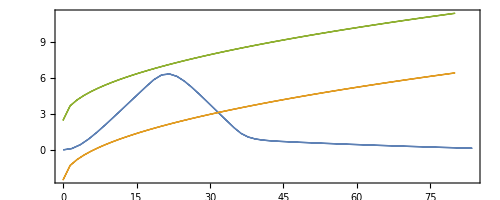

```mathematica
ParametricPlot[{{x[t],y[t]}/.solution,{z,z^(1/2)-2.5},{z,z^(1/2)+2.5}},{z,0,80},{t,0,time},PlotRange-> All]
```